# Analytics of the L3 points (x>1)

Author : Martin Horvat, March 2016

## Definitions

```mathematica
(* Omega = delta*KopalPotential(x = delta t, y=0, z=0), a = F^2 delta^3 *)
Clear[Omega];
Omega[t_,q_,a_]:=1/Abs[t]+q(1/Abs[t-1] -t)+1/2 a(1+q) t^2

(* Omega1 is Omega[1+t] for t>0 *)
Clear[Omega3];
Omega3[t_,q_,a_]:=1/(t+1)+q(1/t - t-1)+1/2 a(1+q) (t+1)^2

(* Derivative Omega1 *)
Clear[dOmega3];
dOmega3[t_,q_,a_]=Simplify[Together[D[Omega3[t,q,a],t]]]
```

(q (1+t)^2 (-1+(-1+a) t^2+a t^3)+t^2 (-1+a (1+t)^3))/(t^2 (1+t)^2)

```mathematica
Simplify[Together[P3[s/(1-s),t,q]]]
```

(-3 s^4+s^5-t+3 s t+s^3 (3+2 t)+s^2 (-1+q-4 t+q t))/(-1+s)^5

```mathematica
(* Polynomials *)
```

```mathematica
Clear[P3];
P3[t_,q_,a_]=-Collect[Expand[Numerator[dOmega3[t,q,a]]],t,Simplify]
```

q+2 q t-(-1+a-2 q+a q) t^2-(-2 q+3 a (1+q)) t^3-(-q+3 a (1+q)) t^4-a (1+q) t^5

```mathematica
Clear[P2]; (* Polynomial for L2 point *)
P2[t_,q_,a_]=1+2 t+t^2-(a+2 q+a q) t^3-(q+2 a (1+q)) t^4-a (1+q) t^5
```

1+2 t+t^2-(a+2 q+a q) t^3-(q+2 a (1+q)) t^4-a (1+q) t^5

```mathematica
Clear[Q3];
Q3[s_,q_,a_]=Collect[Expand[-Numerator[Together[dOmega3[s/(1-s),q,a]]]],s,Simplify]
```

-q+3 q s+(-1+a-4 q+a q) s^2+(3+2 q) s^3-3 s^4+s^5

```mathematica
Collect[Simplify[q P3[t,1/q,a]],t,Simplify]
```

1+2 t+(2+q-a (1+q)) t^2+(2-3 a (1+q)) t^3+(1-3 a (1+q)) t^4-a (1+q) t^5

```mathematica
(*Check : P_L3(t,q,a=1) propto P_L2(t,1/q,a=1)*)
```

```mathematica
Simplify[P2[t,q,1]-q P3[t,1/q,1]]
```

0

```mathematica
DP=Collect[Simplify[q P3[t,1/q,a1]-P2[t,q,a]]/(1+q),t,Simplify]
```

(1-a1) t^2+(2+a-3 a1) t^3+(1+2 a-3 a1) t^4+(a-a1) t^5

```mathematica
Simplify[(DP/.a1->a)]
```

-(-1+a) t^2 (1+t)^2

```mathematica
(* Reparametrization q->1/q *)
```

```mathematica
Clear[P];
P[t_,p_,a_]=Collect[Simplify[p P3[t,1/p,a]],t,Simplify]
```

1+2 t+(2+p-a (1+p)) t^2+(2-3 a (1+p)) t^3+(1-3 a (1+p)) t^4-a (1+p) t^5

```mathematica
Clear[Q];
Q[s_,p_,a_]=Collect[Numerator[-Together[P[s/(1-s),p,a]]],s,Simplify]
```

1-3 s+(4+p-a (1+p)) s^2+(-2-3 p) s^3+3 p s^4-p s^5

```mathematica
Solve[s/(1-s)==t,s]
```

{{s→t/(1+t)}}

```mathematica
(* Horner forms *)
```

```mathematica
CForm[HornerForm[P[t,p,c/(1+p)],t]]
```

1 + t*(2 + t*(2 - c + p + t*(2 - 3*c + t*(1 - 3*c - c*t))))

```mathematica
CForm[HornerForm[D[P[t,p,c/(1+p)],t],t]]
```

2 + t*(4 - 2*c + 2*p + t*(6 - 9*c + t*(4 - 12*c - 5*c*t)))

```mathematica
CForm[HornerForm[Q[t,p,a]/.(4+p-a (1+p))->c,t]]
```

1 + t*(-3 + t*(c + t*(-2 - 3*p + t*(3*p - p*t))))

```mathematica
CForm[HornerForm[D[Q[t,p,a]/.(4+p-a (1+p))->c,t],t]]
```

-3 + t*(2*c + t*(-6 - 9*p + t*(12*p - 5*p*t)))

```mathematica
(* Horner forms a=1*)
```

```mathematica
CForm[HornerForm[P[x,p,1],x]]
```

1 + x*(2 + x*(1 + x*(-1 - 3*p + x*(-2 - 3*p + (-1 - p)*x))))

```mathematica
CForm[HornerForm[D[P[x,p,1],x],x]]
```

2 + x*(2 + x*(-3 - 9*p + x*(-8 - 12*p + (-5 - 5*p)*x)))

```mathematica
CForm[HornerForm[P[1-x,p,1],x]]
```

-7*p + x*(12 + 26*p + x*(-24 - 37*p + x*(19 + 25*p + x*(-7 - 8*p + (1 + p)*x))))

```mathematica
CForm[HornerForm[D[P[1-x,p,1],x],x]]
```

12 + 26*p + x*(-48 - 74*p + x*(57 + 75*p + x*(-28 - 32*p + (5 + 5*p)*x)))

```mathematica
(* Solution *)
```

```mathematica
Clear[Sol]
Sol[p_,a_]:=Module[{t},First[t/.Solve[{P[t,p,a]==0,t>0},t,Reals]]];
```

## Plots

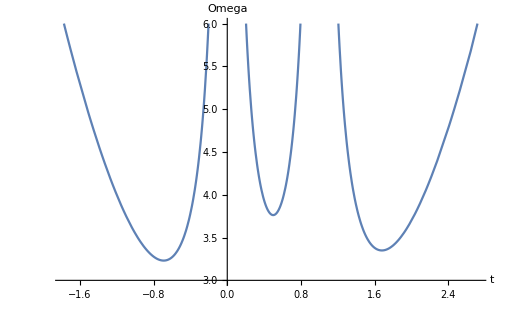

```mathematica
Plot[Omega[t,1,1.05],{t,-2,10},AxesLabel->{"t","Omega"},PlotRange->{All,{3,6}}]
```

```mathematica
qq=0.1;
Sol[1/qq,0.01]+1
```

10.0932

```mathematica
?Omega
```

Global`Omega

Omega[t_]:=1/Abs[t]+q (1/Abs[t-1]-t)+1/2 a (1+q) t^2

```mathematica
FindMinimum[Omega[t,0.1,0.01],{t,1.2}]
```

{-0.338946,{t→10.0932}}

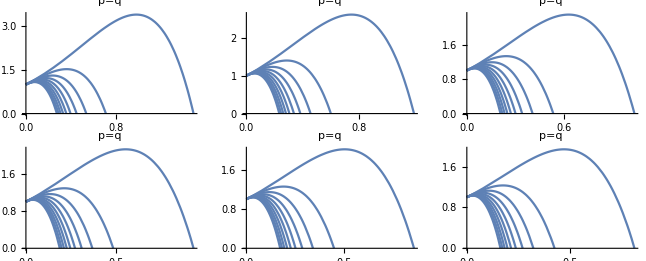

```mathematica
GraphicsGrid[
Partition[
Table[
Plot[
Table[P[t,p,a],{a,0.5,10,1}],
{t,0,4},
PlotRange->{All,{0,Automatic}},
PlotLabel->"p="<>ToString[q],
PlotLabel->{"t","P(t;q,a)"}
],
{p,0.2,3,0.5}],
3
]
]
```

Comment : It is clear that there is only one positive zero!

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve :: ratnz will be suppressed during this calculation.

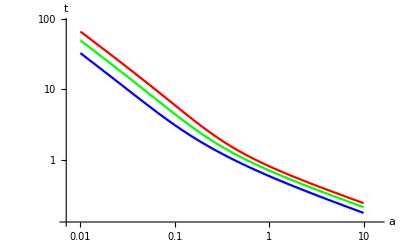

```mathematica
LogLogPlot[{Sol[0.5,a],Sol[1.,a],Sol[2.,a]},{a,0.01,10},PlotRange->All,PlotStyle->{Red,Green,Blue},AxesLabel->{"a","t"}]
```

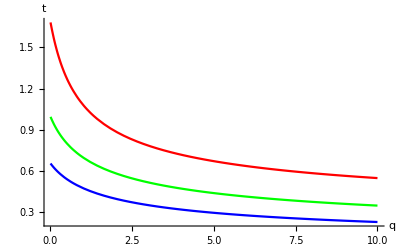

```mathematica
Plot[{Sol[p,0.5],Sol[p,1],Sol[p,2]},{p,0.01,10},PlotRange->All,PlotStyle->{Red,Green,Blue},AxesLabel->{"q","t"}]
```

## a = 1 => this case is same as L2

## q = 1

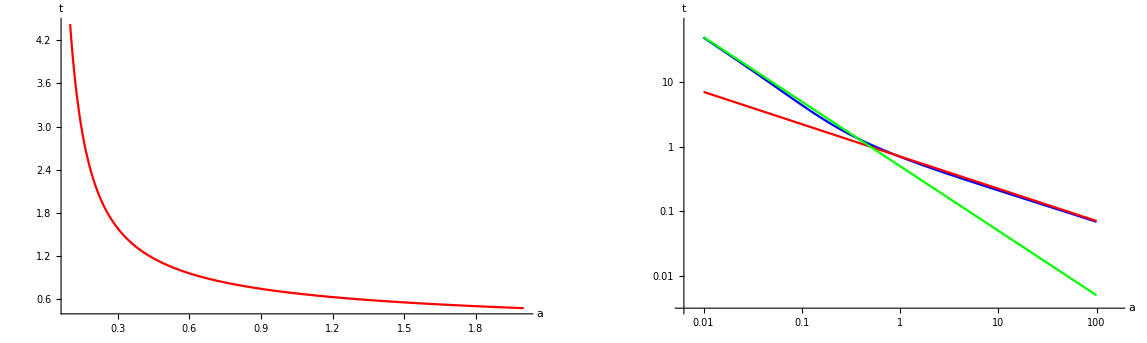

```mathematica
GraphicsGrid[
{
{
Plot[Sol[1,a],{a,0.1,2},PlotRange->All,PlotStyle->Red,AxesLabel->{"a","t"}],
LogLogPlot[{Sol[1,a],(2a)^(-1/2),(2a)^(-1)},{a,0.01,100},PlotRange->All,PlotStyle->{Blue,Red,Green},AxesLabel->{"a","t"}]
}
}]
```

### a -> ∞

Using Q:

Q[s,p,a] = Q1[s,p]+ b Q2[s,p] = 0

t=s/(1-s)

1/b =- Q2[s,p]/Q1[s,p]
b=a(1+p)

```mathematica
?Q
```

Global`Q

Q[s_,p_,a_]=1-3 s+(4+p-a (1+p)) s^2+(-2-3 p) s^3+3 p s^4-p s^5

```mathematica
R1[s_]=Simplify[-D[Q[s,1,a]/.a->b/2,b]/Q[s,1,0]]
```

-s^2/((-1+s) (1-s+s^2)^2)

```mathematica
H1[w_]=Simplify[Normal[InverseSeries[Series[R1[s],{s,0,8}],z]]/.z->w^2,w>0]
```

w-(3 w^2)/2+(29 w^3)/8-10 w^4+(3831 w^5)/128-(189 w^6)/2+(317189 w^7)/1024

```mathematica
Block[{p,a,b,w,s},
a=4.;

b=2a;
w=b^(-1/2);

s=H1[w];

{s/(1-s),Sol[1,a]}
]
```

{0.573992,0.331686}

```mathematica
?P
```

Global`P

P[t_,p_,a_]=1+2 t+(2+p-a (1+p)) t^2+(2-3 a (1+p)) t^3+(1-3 a (1+p)) t^4-a (1+p) t^5

Using P :
   
  P[t, p, a] = P1[t, p] + b P2[t, p] = 0
  
  1/b = - P2[t, p]/P1[t, p]
  
  b = a (1 + p)

```mathematica
?Q
```

Global`Q

Q[s_,p_,a_]=1-3 s+(4+p-a (1+p)) s^2+(-2-3 p) s^3+3 p s^4-p s^5

```mathematica
R2[t_]=-Simplify[D[P[t,1,a]/.a->b/2,b]/P[t,1,0]]
```

(t^2 (1+t)^3)/((1+t+t^2)^2)

```mathematica
H2[w_]=Simplify[Normal[InverseSeries[Series[R2[t],{t,0,8}],z]]/.z->w^2,w>0]
```

w-w^2/2+(13 w^3)/8-4 w^4+(1495 w^5)/128-36 w^6+(118805 w^7)/1024

```mathematica
Block[{p,a,b,w,t},
p=1;
a=4.;

b=a(1+p);
w=b^(-1/2);

t=H2[w];

{t,Sol[p,a]}
]
```

{0.374694,0.331686}

Comment : These are not really good approximations!

A different approach:
R2[t] = f[t]^2 (1+t)^3 = 1/b

f(t) = t/(1+t+t^2)

```mathematica
{f1,f2}=t/.Solve[f(1+t+t^2) == t, t]
```

{(1-f-√(1-2 f-3 f^2))/(2 f),(1-f+√(1-2 f-3 f^2))/(2 f)}

```mathematica
Simplify[f1*f2]
```

1

```mathematica
SF[f_]:=(2f)/(1-f+√(1-2 f-3 f^2))
```

```mathematica
Block[{f,t,a,p,b},
p=1;
a=4.;
b=Sqrt[2a];
t=1/b;
Do[
f=1/(b*(1+t)^(3/2));
t=SF[f],
{10}];
{t,Sol[p,a]}
]
```

{0.331827,0.331686}

```mathematica
R2[0.4746469134448299]
```

0.25

```mathematica
1/(2*2.)
```

0.25

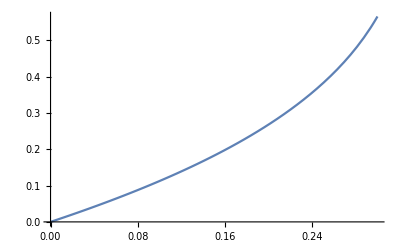

```mathematica
Plot[SF[f],{f,0,0.3}]
```

A different approach:
R2[t] = g[t]^2 (1+t) = 1/b

g(t) = t(1+t)/(1+t+t^2)

```mathematica
{g1,g2}=t/.Solve[g(1+t+t^2) == t(1+t), t]
```

{(1-g-√(1+2 g-3 g^2))/(2 (-1+g)),(1-g+√(1+2 g-3 g^2))/(2 (-1+g))}

```mathematica
Simplify[g1*g2]
```

g/(-1+g)

```mathematica
SG[g_]=(2g)/(1-g+√(1+2 g-3 g^2));
```

```mathematica
Block[{g,t,a,p,b},
p=1;
a=2.; 
b=Sqrt[2a];
t=1/b;
Do[
g=1/(b*(1+t)^(1/2));
t=SG[g],
{4}];
{t,Sol[p,a]}
]
```

{0.474693,0.474647}

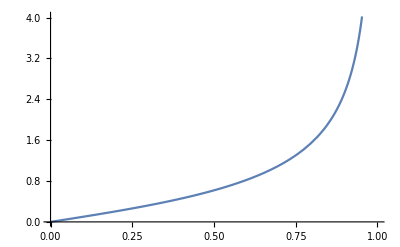

```mathematica
Plot[SG[f],{f,0,1}]
```

These last approach should work for all a > 1/2

### a -> 0

Using P :
 2a=u (1+u+u^2)^2/(1+u)^3
 t = 1/u

```mathematica
H3[z_]=Normal[InverseSeries[Series[u (1+u+u^2)^2/(1+u)^3,{u,0,9}],z]]
```

z+z^2-z^3-5 z^4+33 z^6+41 z^7-211 z^8-625 z^9

```mathematica
Block[{a,s},
a=0.1;
b=2*a;
s=H3[b];
{1/s,Sol[1,a]}
]
```

{4.42916,4.42521}

Comment : Does not work too good, only for a << 1 (e.g. a < 0.1)

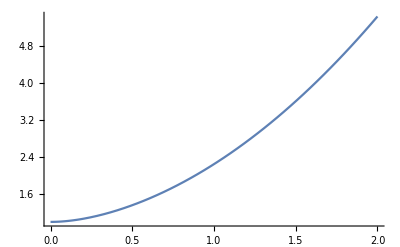

```mathematica
Plot[(1+u+u^2)^2/(1+u)^2,{u,0,2},PlotRange->All]
```

Iterative approach!

```mathematica
Block[{a,b,u,v},
a=0.4;
b=2*a;
u=b;
Do[
v=b/(((1+u+u^2)/(1+u))^2);
u=v/(1-v),
{10}];

{1/u,Sol[1,a]}
]
```

{0.745383,1.26901}

Comment : Not that good!

Writing P[1/u] in the form:
	b = 2 a = u (1 + u) G[u]
	G[u] = ((1+u+u^2)/(1+2u+u^2))^2

Iteration:
	b/G[u_n] = u_{n+1}(1+u_{n+1})

```mathematica
SK[e_]=2e/(Sqrt[1+4e]+1);
Block[{a,b,u,v},
a=1.;
b=2*a;
u=b;
Do[
v=b*((1+2u+u^2)/(1+u+u^2))^2;
u=SK[v],
{4}];

{1/u,Sol[1,a]}
]
```

{0.698398,0.698406}

Comment : Works nicely!

### a ≈ 1

Using P : 

2 (a-1) =R[t0+u]

R[t0]=2;

R[t]=(1 +  t+ t^2)^2/(t^2(1 + t)^3)

```mathematica
t01=N[Sol[1,1]]
```

0.698406

```mathematica
R3[t_]=(1+t+t^2)^2/(t^2(1+t)^3)
```

((1+t+t^2)^2)/(t^2 (1+t)^3)

```mathematica
R3[t01]
```

2.

```mathematica
Series[R3[t01+u],{u,0,9}]
```

0.5+1.21866 u+0.343639 u^2-0.432853 u^3+0.253124 u^4-0.0291678 u^5-0.109618 u^6+0.13879 u^7-0.0959901 u^8+0.0327315 u^9+O[u]^10

```mathematica
H4[z_]=Normal[InverseSeries[Series[R3[t01+u]-2,{u,0,8}],z]]
```

-0.205143 z+0.0907046 z^2-0.0438582 z^3+0.0219484 z^4-0.0111619 z^5+0.00572254 z^6-0.00294574 z^7+0.00151903 z^8

```mathematica
Block[{a,s,b},
a=0.2;
b=2*(a-1);
s=H4[b];
{t01+s,Sol[1,a]}
]
```

{1.93969,2.23774}

## a != 1, q != 1

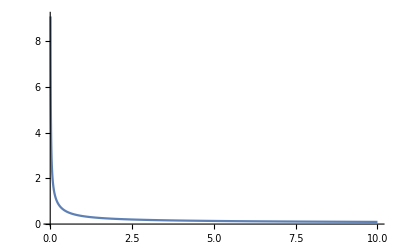

```mathematica
Plot[Sol[10,a],{a,0.01,10},PlotRange->All]
```

### a -> ∞

Rewriting P in into 
	
	R(t,p) = 1/b

where b= a(1+q)

Solving in the sense of iteration

	g(t) = (1+t)^2/(1+t^2+p (t/(1+t))^2)

1/(b g(t_n)) = t_{n+1)^2/(t_{n+1) + 1)

```mathematica
L[t_,p_,b_]=P[t,p,a]/.a(1+p)->b
```

1+2 t+(2-b+p) t^2+(2-3 b) t^3+(1-3 b) t^4-b t^5

```mathematica
L1[t_,p_]=Simplify[-D[L[t,p,b],b]/L[t,p,0]]
```

(t^2 (1+t)^3)/(1+2 t+(2+p) t^2+2 t^3+t^4)

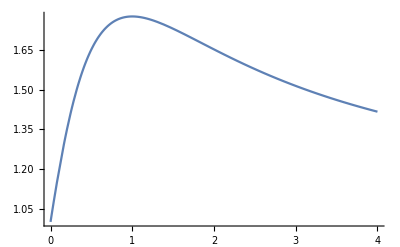

```mathematica
Plot[((1+t)^3(1+t))/(1+2 t+(2+p) t^2+2 t^3+t^4)/.p->1,{t,0,4}]
```

```mathematica
SH[e_]=(e+Sqrt[e^2+4e])/2
```

1/2 (e+√(4 e+e^2))

```mathematica
Block[{a,b,p,g,t,e},
a=0.001;
p=1000;
b=a(1+p);
t=1/Sqrt[b];
Do[
g=(1+t)^2/(1+t^2+p(t/(1+t))^2);
e=1/(b g);
t=SH[e];
,{10}
];
{t,Sol[p,a]}
]
```

{1.97765,9.34509}

Comment : Does not work well for big p, and this is emphasized for small a!

### a -> 0

```mathematica
J[u_,p_,b_]=P[1/u,p,a]/.a(1+p)->b
```

1-b/u^5+(1-3 b)/u^4+(2-3 b)/u^3+(2-b+p)/u^2+2/u

```mathematica
J1[u_,p_]=Simplify[-J[u,p,0]/D[J[u,p,b],b]]
```

(u (1+2 u+(2+p) u^2+2 u^3+u^4))/(1+u)^3

```mathematica
Simplify[1+2 u+(2+p) u^2+2 u^3+u^4/.p->1]
```

(1+u+u^2)^2

We find that for all q the root diverges as we go into a->0

Solving via iteration:

	b:=a(1+q)
	t:=1/u

	b= u(1+u) g(u,p)

	g(u,p) = (1+u^2)/(1+u)^2+p (u/(1+u)^2)^2

Iteration:
	b/g(u_n,p) = u_{n+1}(1+u_{n+1})

```mathematica
SK[e_]=2e/(Sqrt[1+4e]+1);
Block[{a,b,p,g,u,v},
a=0.0001;
p=0.1;
b=a(1+p);
u=b;
Do[
g=(1+u^2)/(1+u)^2+p u^2/(1+u)^4;
v=b/g;
u=SK[v],
{4}
];

{1/u,Sol[p,a]}
]
```

{9089.91,9089.91}

Comment : The iteration for a -> oo and a -> 0 are exactly the same!!!! Does not work well for big p, and this is emphasized for small a!

```mathematica
s1=1-0.01^(2/3)
```

0.953584

```mathematica
s1/(1-s1)
```

20.5443

### p -> 0

R[t, a] = -P[t, 0, a]/D[P[t, p, a]] = p

R[t0 +u, a] =T[u,a] where R[t0]= 0. R[t]=0 is cubic equation

Inverting T[u,a] = q gives us u.

t = t0+u

```mathematica
Simplify[P[t,0,a]]
```

-(1+t)^2 (-1+(-1+a) t^2+a t^3)

```mathematica
t/.Solve[-1+(-1+a) t^2+a t^3 == 0,t]
```

{-(-1+a)/(3 a)+(2^(1/3) (-1+a)^2)/(3 a (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))+((2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))/(3 2^(1/3) a),-(-1+a)/(3 a)-((1+ⅈ √3) (-1+a)^2)/(3 2^(2/3) a (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))-((1-ⅈ √3) (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))/(6 2^(1/3) a),-(-1+a)/(3 a)-((1-ⅈ √3) (-1+a)^2)/(3 2^(2/3) a (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))-((1+ⅈ √3) (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))/(6 2^(1/3) a)}

```mathematica
t02[1]
```

1

```mathematica
t02[a_]=FullSimplify[-(-1+a)/(3 a)+(2^(1/3) (-1+a)^2)/(3 a (2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))+((2-6 a+33 a^2-2 a^3+3 √3 √(4 a^2-12 a^3+39 a^4-4 a^5))^(1/3))/(3 2^(1/3) a)]
```

1/(6 a)(2-2 a+(2 2^(1/3) (-1+a)^2)/((2+a (-6+(33-2 a) a)+3 √3 √(a^2 (4+a (-12+(39-4 a) a))))^(1/3))+2^(2/3) (2+a (-6+(33-2 a) a)+3 √3 √(a^2 (4+a (-12+(39-4 a) a))))^(1/3))

```mathematica
R5[t_,a_]=Simplify[-P[t,0,a]/D[P[t,p,a],p]]
```

-((1+t)^2 (-1+(-1+a) t^2+a t^3))/(t^2 (-1+a (1+t)^3))

Solving:
-1 + (-1+a) t^2 + a t^3 == 0
as a cubic equation
  x^3+b x^2+c x + d = 0

```mathematica
SolveCubic2[a_]:=Module[{b,c,d,p,q,A,phi,dd,sd,t},
If[a==1,Return[1]];

b=(a-1)/a;
c=0;
d=-1/a;

p=c-b^2/3;
q=d+b(2b^2/27-c/3);

dd=p^3/27+q^2/4;
A=2*Sqrt[Abs[p]/3];

If[dd≤0,
phi=ArcCos[3*q/(A*p)];
Return[A*Cos[phi/3]-b/3];
];

If [p<0,
phi=ArcCosh[-3*Abs[q]/(A*p)];
Return[-A*Sign[q]Cosh[phi/3]-b/3];
];

phi=ArcSinh[3*q/(A*p)];
Return[-A*Sinh[phi/3]-b/3]
];
```

```mathematica
Block[{b,a,c,d,p,q,dd},
b=(a-1)/a;
c=0;
d=-1/a;

p=c-b^2/3;
q=d+b(2b^2/27-c/3);
dd=p^3/27+q^2/4;
FullSimplify[{p,q,dd}]
]
```

{-(-1+a)^2/(3 a^2),(2 (-1+a)^3)/(27 a^3)-1/a,(4+a (-12+(39-4 a) a))/(108 a^4)}

```mathematica
SolveCubic2[10.]
```

0.289898

```mathematica
t/.Solve[((-1+(-1+a) t^2+a t^3)/.a->10.) == 0,t]
```

{-0.689898,-0.5,0.289898}

```mathematica
t02[10.]
```

0.289898-1.4803×10^-17 ⅈ

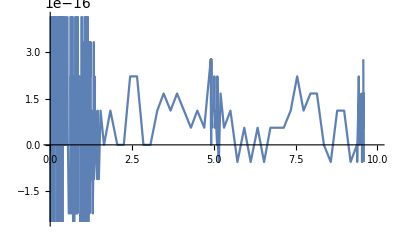

```mathematica
Plot[SolveCubic2[a]-t02[a],{a,0.01,10}]
```

```mathematica
DR5[t_,a_]=FullSimplify[Table[D[R5[t,a],{t,n}]/n!,{n,1,3}]];
```

```mathematica
CForm/@FullSimplify[DR5[t,a]*Table[t^(3+i) (-1+a (1+t)^3)^(2+i),{i,0,2}]]
```

{-((1 + t)*(-2 + 2*Power(t,3) + a*(1 + t)*(2 + t*(7 + t*(8 + t*Power(1 + t,2)))))),3 + 2*t + Power(t,4) + Power(a,2)*Power(1 + t,4)*(3 + t*(14 + t*(25 + t*(20 + t*Power(1 + t,2))))) + a*(1 + t)*(-6 + t*(-22 + t*(-23 + t*(-4 + 7*t*Power(1 + t,2))))),2*(2 + t) - a*(12 + t*(51 + 2*t*(36 + t*(20 + t*(4 + 5*t*Power(1 + t,2))))) + Power(a,2)*Power(1 + t,6)*(4 + t*(23 + t*(54 + t*(65 + t*(40 + t*Power(1 + t,2)))))) + 4*a*Power(1 + t,3)*(-3 + t*(-15 + t*(-27 + t*(-17 + 2*t*(1 + 2*t*Power(1 + t,2)))))))}

```mathematica
Block[{t0,F,p,a,x,z,u,t},
a=100000000.;
p=0.01;
t0=Chop[t02[a]];
F=DR5[t0,a];
u=Normal[InverseSeries[SeriesData[x,0,F,1,Length[F]+1,1],z]]/.z->p;
t=Sol[p,a];
{t0,t0+u,t,Abs[1-(t0+u)/t]}
]
```

{0.000099995,0.0000994988,0.0000994988,2.72325×10^-9}

Comment : It seems it works fine for sufficiently small p, for all a.

```mathematica
(as^(-1/3)-1)
```

{20.5443,9.,3.64159,1.15443}

### p ->∞

```mathematica
as^(-1/3)
```

{46.4159,21.5443,10.,4.64159,2.15443}

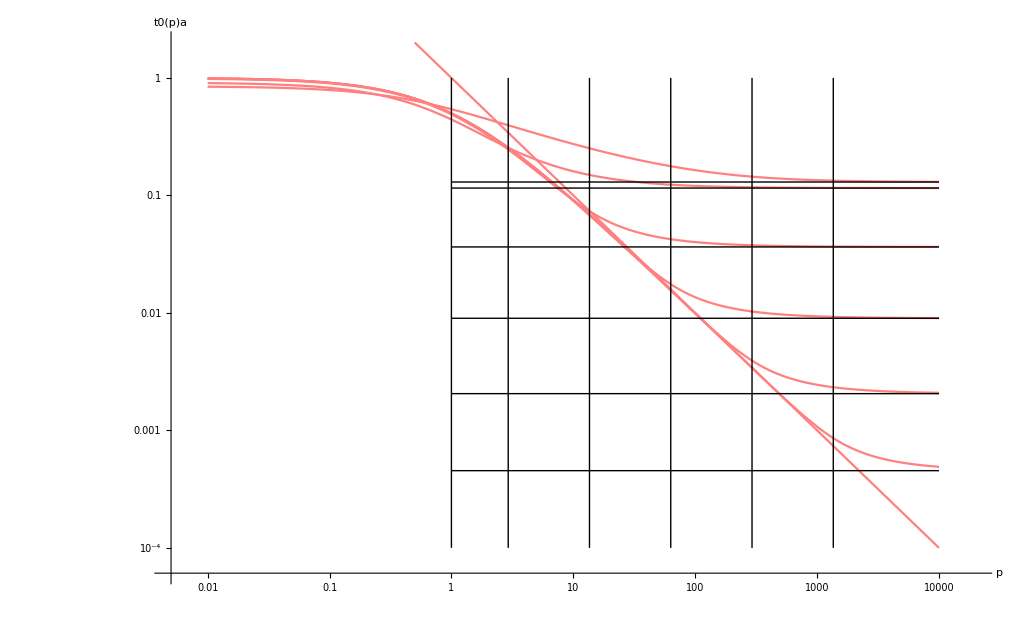

```mathematica
as={10.^-5,0.0001,0.001,0.01,0.1,0.5};
vs={3,12,50,250};
LogLogPlot[
Append[Map[Sol[p,#]#&,as],p^(-1)],
{p,0.01,10000},
PlotRange->{All,{Automatic,2}},
PlotStyle->{Red,Green,Blue,Pink},
AxesLabel->{"p","t0(p)a"},
Epilog->{
Union[
Line[{Log@{#,10^-4},Log@{#,1}}]&/@((2 as)^(-2/3)),
Line[{Log@{1,#},Log@{10^4,#}}]&/@(as*(as^(-1/3)-1))
]
}
]
```

Comment : It is clear that for a < 1 the solution  t in [a^(-1/3) - 1, 1/a]

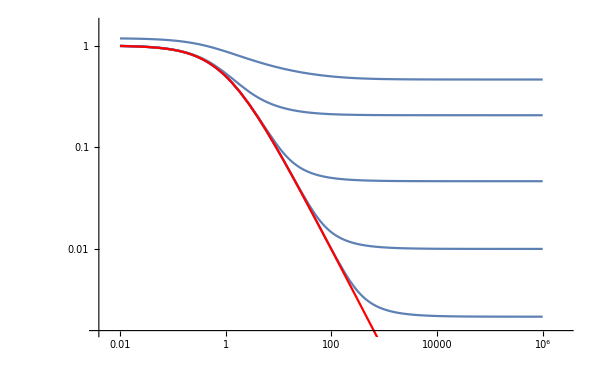

```mathematica
Block[{as1},
as1={0.5,0.1,0.01,0.001,0.0001};
Show[
LogLogPlot[Sol[p,#]*#+#/(1+#)&/@as1,{p,0.01,10^6},PlotRange->All],
LogLogPlot[1/(1+p),{p,0.01,10^6},PlotRange->All,PlotStyle->Red]
]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

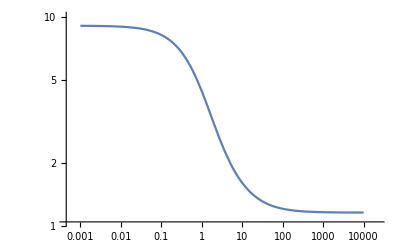

```mathematica
LogLogPlot[Sol[p,0.1],{p,0.001,10000},PlotRange->All]
```

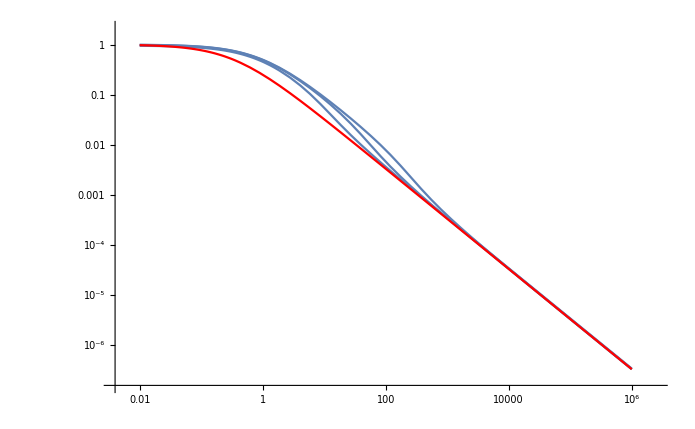

```mathematica
Block[{as1},
as1={0.01,0.001,0.0001};
Show[
LogLogPlot[(Sol[p,#]-(#^(-1/3)-1))*#&/@as1,{p,0.01,10^6},PlotRange->All],
LogLogPlot[1/(1+3p),{p,0.01,10^6},PlotRange->All,PlotStyle->Red]
]
]
```

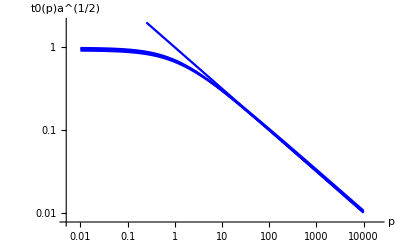

```mathematica
LogLogPlot[
Append[Table[Sol[p,a]Sqrt[a],{a,{10,100,1000}}],p^(-1/2)],
{p,0.01,10000},
PlotRange->{All,{Automatic,2}},
PlotStyle->{Red,Green,Blue},
AxesLabel->{"p","t0(p)a^(1/2)"}
]
```

#### Iterative approach using Q

```mathematica
R4[s_,a_]=Simplify[-D[P[s/(1-s),p,a],p]/P[s/(1-s),0,a]]
```

-((a+(-1+s)^3) s^2)/(-1+3 s+(-4+a) s^2+2 s^3)

Solving 

1/q = R[s,a]

R[s,a]=((a-(1-s)^3) s^2)/(1-3 s+(4-a) s^2-2 s^3)=(c-(1-s))s^2 G(s,a)   G(s,a)= (c^2+(1-s)c+(1-s)^2)/ (1-3s+(4-a)s^2-2s^3)
with iteration

z= 1/(G(s_n, a) q)
(s_{n+1}+c-1)s_{n+1}^2 = z

where c=a^(1/3)

```mathematica
SD[z_,c_]:=Module[{s},s/.NSolve[{s^2(s-1+c)==z,0<s},s][[1]]]
```

```mathematica
Block[{p,a,c,tasym,s,z},
a=0.5;
p=100;
c=1-a^(1/3);
tasym=a^(-1/3)-1;
Print["p_{crit}=",(2 a)^(-2/3)," t_{asymp}=",tasym];
s=0;
Do[
z=(1-3s+(4-a)s^2-2s^3)/(p(c^2+c(1-s)+(1-s)^2));
s=SD[z,c];
Print[z," ",s],
{4}];

{s/(1-s),a^(-1/3)-1.,Sol[p,a]}
]
```

p_{crit}=1. t_{asymp}=0.259921

0.00800731 0.806026

-0.0159331 0.15836

0.00654103 0.803824

-0.0155339 0.156085

{0.184953,0.259921,0.327656}

Comment : 

This iterations is not very efficient! 

If does not work well for a near to 1 and this is emphasized for small q.

Actully is does not work well for all q of the order and smaller than q_{crit}=(2a)^(-2/3).

Works well for q >> q_{crit}.

#### Approach with an empirical formula

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

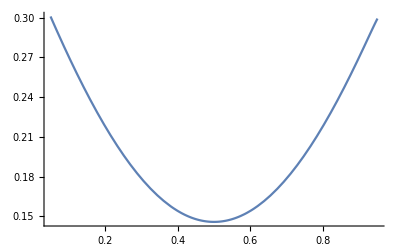

```mathematica
Plot[(Sol[p,c^3]-1/c+1)*p*c^3(1-c)^2/.p->10^6,{c,0.05,0.95}]
```

```mathematica
data1=Table[{c,(Sol[p,c^3]-1/c+1)*(p+1/3)*c^3(1-c)^2/.p->10^6},{c,0.03,0.97,0.01}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

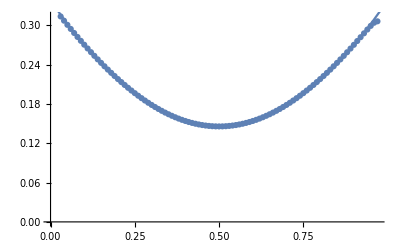

```mathematica
Show[ListPlot[data1],Plot[f3[c],{c,0,1}]]
```

```mathematica
f3[c_]=Fit[data1,{1,(c-1/2)^2},c]
```

0.147468+0.764465 (-1/2+c)^2

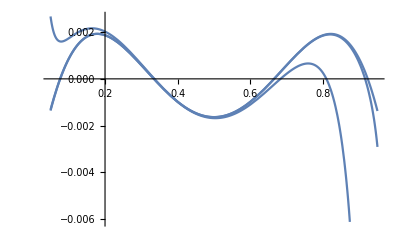

```mathematica
Plot[
Table[
(Sol[p,c^3]-1/c+1)*(p+1/3)*c^3(1-c)^2-f3[c],{p,{10^4,10^6,10^8}}],{c,0.05,0.95}]
```

```mathematica
Sol1[p_,a_]=With[{c=a^(1/3)},f3[c]/((p +1/3)c^3(1-c)^2)+1/c-1];
```

```mathematica
Sol1[100,0.02^2]
```

20.8889

```mathematica
Sol[100,0.02^2]
```

26.9541

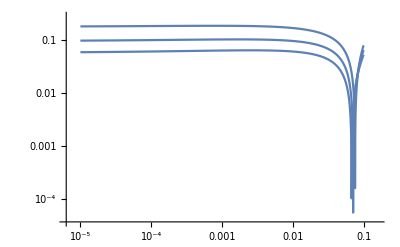

```mathematica
LogLogPlot[
Block[{p,u,c,t,dt1,dt2,dt3,kk},
p=(2*a)^(-2/3);
t=Sol1[p,a];
dt1=Abs[(t/Sol[p,a]-1)];

p=1.5*(2*a)^(-2/3);
t=Sol1[p,a];
dt2=Abs[(t/Sol[p,a]-1)];


p=2*(2*a)^(-2/3);
t=Sol1[p,a];
dt3=Abs[(t/Sol[p,a]-1)];

{dt1,dt2,dt3}
],{a,10^-5,0.1},PlotRange->All]
```

#### Expansiong approach using Q

```mathematica
Clear[DR4]
DR4[u_,c_]=FullSimplify[Series[R4[1-c+u,c^3],{u,0,2}],c>0]
```

-(3 ((-1+c)^2 c) u)/(-1+(-2+c) (-1+c) c (1+c))+(3 (-1+c) c^2 (-3+c (3+(-3+c) c)) u^2)/(-1+(-2+c) (-1+c) c (1+c))^2+O[u]^3

```mathematica
H5[w_,c_]=Normal[Series[FullSimplify[Normal[InverseSeries[DR4[u,c],w]],w>0&&1>c>0],{w,0,2}]]
```

((1-2 c+c^2+2 c^3-c^4) w)/(3 (-1+c)^2 c)+((-3+3 c-3 c^2+c^3) (-1+(-2+c) (-1+c) c (1+c)) w^2)/(9 (-1+c)^5 c)

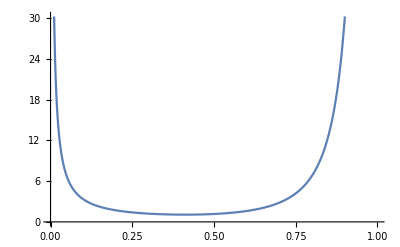

```mathematica
Plot[D[H5[w,c],w]/.w->0,{c,0,1}]
```

```mathematica
Block[{a,p,u,c,s},
a=0.1;
p=100;
c=a^(1/3);
u=H5[1/p,c];
s=(1-c)+u;
{(2*a)^(-2/3),1-c,s/(1-s),Sol[p,a]}]
```

{2.92402,0.535841,1.20434,1.20452}

Trying to optimize with a shift!

```mathematica
R6[s_,a_]=Simplify[-D[P[s/(1-s),p,a],p]/P[s/(1-s),-k,a]]
```

((a+(-1+s)^3) s^2)/(1-3 s+(4+a (-1+k)-k) s^2+(-2+3 k) s^3-3 k s^4+k s^5)

```mathematica
Clear[DR6]
DR6[u_,c_]=FullSimplify[Series[R6[1-c+u,c^3],{u,0,3}],c>0]
```

-(3 ((-1+c)^2 c) u)/(-1+(-2+c) (-1+c) c (1+c))+(3 c^2 (3-6 c+6 c^2-4 c^3+c^4-3 (-1+c)^4 k) u^2)/(-1+(-2+c) (-1+c) c (1+c))^2+((-1+c (6-c (15+c (-34+c (78+c (-94+c (67+(-4+c) c (9+(-2+c) c))))))+18 (-1+c)^3 c^3 (-3+c (3+(-3+c) c)) k-27 (-1+c)^6 c^3 k^2)) u^3)/(c (-1+(-2+c) (-1+c) c (1+c))^3)+O[u]^4

```mathematica
H6[w_,c_]=Normal[Series[FullSimplify[Normal[InverseSeries[DR6[u,c],w]],w>0&&1>c>0],{w,0,2}]]
```

-((-1+(-2+c) (-1+c) c (1+c)) w)/(3 (-1+c)^2 c)-((-1+(-2+c) (-1+c) c (1+c)) (3-3 k+c (3+(-3+c) c) (-1+3 k)) w^2)/(9 (-1+c)^5 c)

```mathematica
H6[w,c]/.k->1
```

-((-1+(-2+c) (-1+c) c (1+c)) w)/(3 (-1+c)^2 c)-(2 (3+(-3+c) c) (-1+(-2+c) (-1+c) c (1+c)) w^2)/(9 (-1+c)^5)

```mathematica
Block[{a,p,u,c,s},
a=0.1;
p=10;
c=a^(1/3);
u=H6[1/(p+k),c]/.k->1/3;
s=(1-c)+u;
{(2*a)^(-2/3),1-c,s/(1-s),Sol[p,a]}]
```

{2.92402,0.535841,1.48622,1.60364}

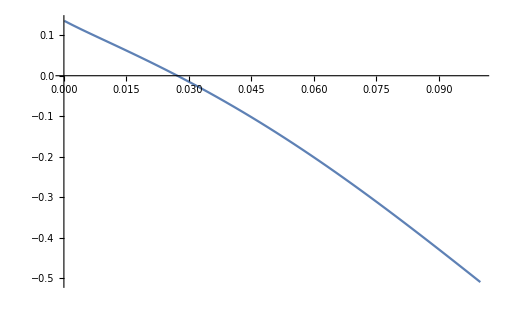

```mathematica
Plot[
Block[{p,u,c,s},
p=(2*a)^(-2/3);
c=a^(1/3);
u=H6[1/(p+k),c]/.k->1;
s=(1-c)+u;
(s/(1-s))/Sol[p,a]-1
],
{a,0.0001,0.1},PlotRange->All
]
```

#### Expansion approach using P

```mathematica
RT6[t_,a_]=Simplify[-D[P[t,p,a],p]/P[t,-k,a]]
```

(t^2 (-1+a (1+t)^3))/(1+2 t+(2+a (-1+k)-k) t^2+(2+3 a (-1+k)) t^3+(1+3 a (-1+k)) t^4+a (-1+k) t^5)

```mathematica
Simplify[Expand[RT6[1/c-1 +u,c^3]]]
```

(c^3 (1+c (-1+u))^2 u (3+3 c u+c^2 u^2))/(1+c^7 (-1+k) (-1+u)^2 u^3+c (-2+4 u)+c^6 (-1+k) u^2 (3-8 u+5 u^2)+c^2 (1-6 u+6 u^2)+c^5 (-1+k) u (3-12 u+10 u^2)+c^3 (2+(-1+3 k) u-6 u^2+4 u^3)+c^4 (-1+(8-6 k) u+(-8+9 k) u^2-2 u^3+u^4))

```mathematica
Collect[(1+c^7 (-1+k) (-1+u)^2 u^3+c (-2+4 u)+c^6 (-1+k) u^2 (3-8 u+5 u^2)+c^2 (1-6 u+6 u^2)+c^5 (-1+k) u (3-12 u+10 u^2)+c^3 (2+(-1+3 k) u-6 u^2+4 u^3)+c^4 (-1+(8-6 k) u+(-8+9 k) u^2-2 u^3+u^4)),u,Simplify]
```

1-2 c+c^2+2 c^3-c^4+c (4-6 c+c^3 (8-6 k)+3 c^4 (-1+k)+c^2 (-1+3 k)) u+c^2 (6-6 c-12 c^3 (-1+k)+3 c^4 (-1+k)+c^2 (-8+9 k)) u^2+c^3 (4-2 c+10 c^2 (-1+k)-8 c^3 (-1+k)+c^4 (-1+k)) u^3+(c^4+5 c^6 (-1+k)-2 c^7 (-1+k)) u^4+c^7 (-1+k) u^5

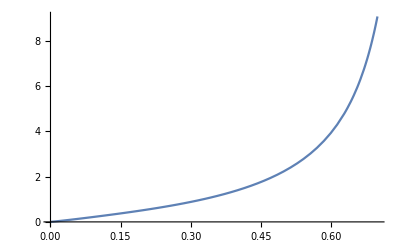

```mathematica
Plot[RT6[1/c-1 +u/c^3,c^3]/.{c->(0.1)^(1/3),k->0},{u,0.0001,0.7}]
```

```mathematica
HRT6[w_,c_]=Collect[Normal[FullSimplify[InverseSeries[Series[RT6[1/c-1 +u,c^3],{u,0,3}],z]]]/.z->w*3(1-c)^2c^3,w,FullSimplify]
```

(1-(-2+c) (-1+c) c (1+c)) w-(c (-1+(-2+c) (-1+c) c (1+c)) (-1+c (3+c (-2 (-2+c) (-1+c) c+3 (-1+c)^3 k))) w^2)/(-1+c)-1/(3 (-1+c)^2)c^2 (-1+(-2+c) (-1+c) c (1+c)) (2+c (-12+c (12+58 c-159 c^2+160 c^3+26 c^4-180 c^5+184 c^6-84 c^7+14 c^8-18 (-1+c)^3 (1+c (-3+2 (-2+c) (-1+c) c^2)) k+27 (-1+c)^6 c^2 k^2))) w^3

```mathematica
Block[{a,p,u,c,w,t},
a=0.004^2;
p=1000;
c=a^(1/3);
w=1/(3(1-c)^2a (p+k))/.k->1;
u=HRT6[w,c]/.k->1;
t=1/c-1+u;
{(2*a)^(-2/3),t,Sol[p,a]}]
```

{992.126,74.2288,72.8864}

```mathematica
Sol[1000,0.0004^2]
```

6242.92

```mathematica
Sol1[1000,0.0004^2]
```

2295.73

```mathematica
(0.004^2)^(-1/3)-1
```

38.685

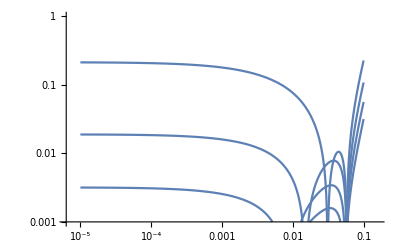

```mathematica
LogLogPlot[
Block[{p,u,c,t,w,dt0,dt1,dt2,dt3,kk},
kk=2;

p=0.5(2*a)^(-2/3);
c=a^(1/3);
w=1/(3(1-c)^2a (p+k))/.k->kk;
u=HRT6[w,c]/.k->kk;
t=1/c-1+u;
dt1=Abs[(t/Sol[p,a]-1)];

p=(2*a)^(-2/3);
c=a^(1/3);
w=1/(3(1-c)^2a (p+k))/.k->kk;
u=HRT6[w,c]/.k->kk;
t=1/c-1+u;
dt0=Abs[(t/Sol[p,a]-1)];

p=1.5*(2*a)^(-2/3);
c=a^(1/3);
w=1/(3(1-c)^2a (p+k))/.k->kk;
u=HRT6[w,c]/.k->kk;
t=1/c-1+u;
dt2=Abs[(t/Sol[p,a]-1)];

p=2*(2*a)^(-2/3);
c=a^(1/3);
w=1/(3(1-c)^2a (p+k))/.k->kk;
u=HRT6[w,c]/.k->kk;
t=1/c-1+u;
dt3=Abs[(t/Sol[p,a]-1)];

{dt0,dt1,dt2,dt3}
],{a,10^-5,0.1},PlotRange->{All,{10^-3,1}}]
```

Comment : It works perhaps better than the approximation using Q

```mathematica
CForm/@HornerForm/@Rest@CoefficientList[FullSimplify[Series[HRT6[z,c]/.k->2,{z,0,3}]],z]
```

{1 + c*(-2 + c*(1 + (2 - c)*c)),(c*(-1 + c*(5 + c*(-13 + c*(27 + c*(-39 + c*(27 + c*(14 + c*(-34 + (20 - 4*c)*c)))))))))/(-1 + c),(Power(c,2)*(2 + c*(-16 + c*(74 + c*(-262 + c*(719 + c*(-1516 + c*(2531 + c*(-3184 + c*(2489 + c*(-164 + c*(-2036 + c*(2380 + c*(-1346 + (400 - 50*c)*c))))))))))))))/(3 + c*(-6 + 3*c))}

### a ≈ 1

```mathematica
R7[t_,p_]=Simplify[-(1+p)P[t,p,1]/D[P[t,p,a],a]]
```

(1+2 t+t^2-(1+3 p) t^3-(2+3 p) t^4-(1+p) t^5)/(t^2 (1+t)^3)

```mathematica
DR7[t_,p_]=Simplify[Table[D[R7[t,p],{t,n}],{n,1,4}]]
```

{-(2+7 t+8 t^2+(4+3 p) t^3+2 t^4+t^5)/(t^3 (1+t)^4),(2 (3+14 t+25 t^2+20 t^3+(7+6 p) t^4+2 t^5+t^6))/(t^4 (1+t)^5),-(6 (4+23 t+54 t^2+65 t^3+40 t^4+(11+10 p) t^5+2 t^6+t^7))/(t^5 (1+t)^6),(24 (5+34 t+98 t^2+154 t^3+140 t^4+70 t^5+(16+15 p) t^6+2 t^7+t^8))/(t^6 (1+t)^7)}

```mathematica
Block[{DR,t0,p,a,w,x,z,u},
p=10.;
a=0.9;
t0=Sol[p,1];
DR=DR7[t0,p];
w=(1+p)(a-1);
u=Normal[InverseSeries[SeriesData[x,0,DR,1,Length[DR]+1,1],z]]/.z->w;
{t0+u,Sol[p,a]}
]
```

{0.373406,0.371221}

Comment : The use of this expansion is very limited!